## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="TPI";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_MASSpy_r.csv";

mainFolder = "fit_TPI_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological,Q10];
```

(dhap^c⇌g3p^c)^TPI

Null; Null

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | dhap | Null | 0.0872761 | 0.0829123
0.09164 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.00103 | 0.00093
0.00113 |  | M | 7.6 | 25 | teoahcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null | 27025.3 | 26523.8
27526.8 | 1/s | 7.6 | 37 | teoahcl | 0.1 | 
1 | dhap | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Ki | 2-phosphoglycolate | 0.006 | 0.0057
0.0063 |  | Competitive | dhap | Null | M | 7.6 | 25 | teoahcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities={0};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(dhap^c⇌g3p^c)^TPI

Null; Null

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | dhap | Null | 0.0872761 | 0.0829123
0.09164 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.00103 | 0.00093
0.00113 |  | M | 7.6 | 25 | teoahcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null | 27025.3 | 26523.8
27526.8 | 1/s | 7.6 | 37 | teoahcl | 0.1 | 
1 | dhap | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_TPI[c] + dhap[c] <=> E_TPI[c]&dhap",
				"E_TPI[c]&dhap <=> E_TPI[c]&g3p",
				"E_TPI[c]&g3p <=> E_TPI[c] + g3p[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((TPI^c)_^+dhap^c⇌(TPI^c&dhap^c)_^)^TPI1,((TPI^c&g3p^c)_^⇌(TPI^c)_^+g3p^c)^TPI2,((TPI^c&dhap^c)_^⇌(TPI^c&g3p^c)_^)^TPI3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((TPI^c)_^+dhap^c⇌(TPI^c&dhap^c)_^)^TPI1,Overscript[(TPI^c&g3p^c)_^⇌(TPI^c)_^+g3p^c, TPI2],((TPI^c&dhap^c)_^⇌(TPI^c&g3p^c)_^)^TPI3}
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

{((TPI^c)_^+dhap^c⇌(TPI^c&dhap^c)_^)^TPI1,((TPI^c&g3p^c)_^⇌(TPI^c)_^+g3p^c)^TPI2,((TPI^c&dhap^c)_^⇌(TPI^c&g3p^c)_^)^TPI3}

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=2;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((TPI^c&dhap^c)_^-((TPI^c&g3p^c)_^)/K_TPI3) Volume_c k_TPI3^⟶}

Volume_c (-(TPI^c&g3p^c)_^ k_TPI3^⟵+(TPI^c&dhap^c)_^ k_TPI3^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
Variables[haldaneRatiosList[[1]]][[1]]
keqValCur = 0.087276143;
haldaneSub = Solve[keqValCur== haldaneRatiosList[[1]],Variables[haldaneRatiosList[[1]]][[1]]];
haldaneSub[[1,1]]
```

k_TPI1^⟵

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

k_TPI1^⟵→(11.4579 k_TPI1^⟶ k_TPI2^⟶ k_TPI3^⟶)/(k_TPI2^⟵ k_TPI3^⟵)

```mathematica
flux = 0.00207;
FluxExpression = absoluteFlux /. {metabolite["dhap", "c"] -> 0.0048,metabolite["g3p","c"]-> 0.0000266,
     parameter["TPI_total"] -> 0.0000176451485555229, parameter["Volume", "c"] -> 1};
```

```mathematica
FluxExpression2 = parameter["v", "TPI"] /. FluxExpression/.haldaneSub[[1,1]];
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{3,FluxExpression2,flux,{0.9*flux,1.1*flux}}};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.087276143
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.087276143
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.087276143
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.087276143
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.087276143
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.087276143
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.087276143
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.087276143
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.087276143
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.087276143
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.087276143
1	0	0.00010300000000000006	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/relRateRev_g3p.txt"	0.09090909090909097
1	0	0.00016324399882349484	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/relRateRev_g3p.txt"	0.1368068886032101
1	0	0.00025872430244548684	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/relRateRev_g3p.txt"	0.2007600089131018
1	0	0.0004100503856701025	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/relRateRev_g3p.txt"	0.28474724895080156
1	0	0.0006498860648145998	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/relRateRev_g3p.txt"	0.3868631798468572
1	0	0.0010300000000000005	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/relRateRev_g3p.txt"	0.5000000000000001
1	0	0.0016324399882349486	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/relRateRev_g3p.txt"	0.6131368201531433
1	0	0.0025872430244548686	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/relRateRev_g3p.txt"	0.7152527510491986
1	0	0.0041005038567010245	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/relRateRev_g3p.txt"	0.7992399910868985
1	0	0.006498860648145998	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/relRateRev_g3p.txt"	0.8631931113967901
1	0	0.010300000000000005	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/relRateRev_g3p.txt"	0.9090909090909092
1	0	1	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateRev.txt"	27025.299764582207
1	0	1	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateRev.txt"	27025.299764582207
1	0	1	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateRev.txt"	27025.299764582207
1	0	1	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateRev.txt"	27025.299764582207
1	0	1	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateRev.txt"	27025.299764582207
1	0	1	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateRev.txt"	27025.299764582207
1	0	1	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateRev.txt"	27025.299764582207
1	0	1	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateRev.txt"	27025.299764582207
1	0	1	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateRev.txt"	27025.299764582207
1	0	1	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateRev.txt"	27025.299764582207
1	0	1	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateRev.txt"	27025.299764582207
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/customRatio_1.txt"	0.00207
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/customRatio_1.txt"	0.00207
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/customRatio_1.txt"	0.00207
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/customRatio_1.txt"	0.00207
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/customRatio_1.txt"	0.00207
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/customRatio_1.txt"	0.00207
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/customRatio_1.txt"	0.00207
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/customRatio_1.txt"	0.00207
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/customRatio_1.txt"	0.00207
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/customRatio_1.txt"	0.00207
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/customRatio_1.txt"	0.00207

### Simulate data with uncertainty

```mathematica
Null
```

```mathematica
Null
```

### Parameter scan

```mathematica
Null
```

```mathematica
Null
```

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/relRateFor_dhap.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/relRateRev_g3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/relRateFor_dhap.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/relRateRev_g3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TPI_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 3.86274980219
best_fit: 3.86221783999
best_fit: 3.86223825281
best_fit: 3.86222884891
best_fit: 4.01097944933
best_fit: 3.86221024642
best_fit: 3.86221030607
best_fit: 3.8622184402
best_fit: 3.86221008415
best_fit: 3.86223344941

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_typeII/input/FBA2.dat⟦2⟧ is longer than depth of object.

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.000117979 | 1.3919×10^-8 | 0.0000237123 | 0.0271693 | 0.0872761 | 0.0872999
1 | haldaneRatio_1 | 0.000117979 | 1.3919×10^-8 | 0.0000237123 | 0.0271693 | 0.0872761 | 0.0872999
1 | haldaneRatio_1 | 0.000117979 | 1.3919×10^-8 | 0.0000237123 | 0.0271693 | 0.0872761 | 0.0872999
1 | haldaneRatio_1 | 0.000117979 | 1.3919×10^-8 | 0.0000237123 | 0.0271693 | 0.0872761 | 0.0872999
1 | haldaneRatio_1 | 0.000117979 | 1.3919×10^-8 | 0.0000237123 | 0.0271693 | 0.0872761 | 0.0872999
1 | haldaneRatio_1 | 0.000117979 | 1.3919×10^-8 | 0.0000237123 | 0.0271693 | 0.0872761 | 0.0872999
1 | haldaneRatio_1 | 0.000117979 | 1.3919×10^-8 | 0.0000237123 | 0.0271693 | 0.0872761 | 0.0872999
1 | haldaneRatio_1 | 0.000117979 | 1.3919×10^-8 | 0.0000237123 | 0.0271693 | 0.0872761 | 0.0872999
1 | haldaneRatio_1 | 0.000117979 | 1.3919×10^-8 | 0.0000237123 | 0.0271693 | 0.0872761 | 0.0872999
1 | haldaneRatio_1 | 0.000117979 | 1.3919×10^-8 | 0.0000237123 | 0.0271693 | 0.0872761 | 0.0872999
1 | haldaneRatio_1 | 0.000117979 | 1.3919×10^-8 | 0.0000237123 | 0.0271693 | 0.0872761 | 0.0872999
1 | relRateRev_g3p | 0.0154895 | 0.000239924 | 0.00330087 | 3.63095 | 0.0909091 | 0.09421
1 | relRateRev_g3p | 0.0147165 | 0.000216577 | 0.00471529 | 3.44668 | 0.136807 | 0.141522
1 | relRateRev_g3p | 0.0136418 | 0.000186099 | 0.00640625 | 3.191 | 0.20076 | 0.207166
1 | relRateRev_g3p | 0.0122345 | 0.000149682 | 0.00813564 | 2.85714 | 0.284747 | 0.292883
1 | relRateRev_g3p | 0.0105294 | 0.000110869 | 0.0094941 | 2.45412 | 0.386863 | 0.396357
1 | relRateRev_g3p | 0.00864818 | 0.0000747911 | 0.0100564 | 2.01128 | 0.5 | 0.510056
1 | relRateRev_g3p | 0.00677504 | 0.0000459012 | 0.00964 | 1.57224 | 0.613137 | 0.622777
1 | relRateRev_g3p | 0.00509128 | 0.0000259211 | 0.00843432 | 1.17921 | 0.715253 | 0.723687
1 | relRateRev_g3p | 0.00371131 | 0.0000137738 | 0.00685926 | 0.858222 | 0.79924 | 0.806099
1 | relRateRev_g3p | 0.00266345 | 7.09395×10^-6 | 0.00531007 | 0.615166 | 0.863193 | 0.868503
1 | relRateRev_g3p | 0.00191297 | 3.65947×10^-6 | 0.00401318 | 0.44145 | 0.909091 | 0.913104
1 | absRateRev | 0.00603741 | 0.0000364503 | 378.32 | 1.39987 | 27025.3 | 27403.6
1 | absRateRev | 0.00603741 | 0.0000364503 | 378.32 | 1.39987 | 27025.3 | 27403.6
1 | absRateRev | 0.00603741 | 0.0000364503 | 378.32 | 1.39987 | 27025.3 | 27403.6
1 | absRateRev | 0.00603741 | 0.0000364503 | 378.32 | 1.39987 | 27025.3 | 27403.6
1 | absRateRev | 0.00603741 | 0.0000364503 | 378.32 | 1.39987 | 27025.3 | 27403.6
1 | absRateRev | 0.00603741 | 0.0000364503 | 378.32 | 1.39987 | 27025.3 | 27403.6
1 | absRateRev | 0.00603741 | 0.0000364503 | 378.32 | 1.39987 | 27025.3 | 27403.6
1 | absRateRev | 0.00603741 | 0.0000364503 | 378.32 | 1.39987 | 27025.3 | 27403.6
1 | absRateRev | 0.00603741 | 0.0000364503 | 378.32 | 1.39987 | 27025.3 | 27403.6
1 | absRateRev | 0.00603741 | 0.0000364503 | 378.32 | 1.39987 | 27025.3 | 27403.6
1 | absRateRev | 0.00603741 | 0.0000364503 | 378.32 | 1.39987 | 27025.3 | 27403.6
1 | absRateFor | 0.56147 | 0.315248 | 79.3669 | 264.309 | 30.0281 | 109.395
1 | absRateFor | 0.56147 | 0.315248 | 79.3669 | 264.309 | 30.0281 | 109.395
1 | absRateFor | 0.56147 | 0.315248 | 79.3669 | 264.309 | 30.0281 | 109.395
1 | absRateFor | 0.56147 | 0.315248 | 79.3669 | 264.309 | 30.0281 | 109.395
1 | absRateFor | 0.56147 | 0.315248 | 79.3669 | 264.309 | 30.0281 | 109.395
1 | absRateFor | 0.56147 | 0.315248 | 79.3669 | 264.309 | 30.0281 | 109.395
1 | absRateFor | 0.56147 | 0.315248 | 79.3669 | 264.309 | 30.0281 | 109.395
1 | absRateFor | 0.56147 | 0.315248 | 79.3669 | 264.309 | 30.0281 | 109.395
1 | absRateFor | 0.56147 | 0.315248 | 79.3669 | 264.309 | 30.0281 | 109.395
1 | absRateFor | 0.56147 | 0.315248 | 79.3669 | 264.309 | 30.0281 | 109.395
1 | absRateFor | 0.56147 | 0.315248 | 79.3669 | 264.309 | 30.0281 | 109.395
3 | customRatio_1 | 0.0630066 | 0.00396983 | 0.000279543 | 13.5045 | 0.00207 | 0.00179046
3 | customRatio_1 | 0.0630066 | 0.00396983 | 0.000279543 | 13.5045 | 0.00207 | 0.00179046
3 | customRatio_1 | 0.0630066 | 0.00396983 | 0.000279543 | 13.5045 | 0.00207 | 0.00179046
3 | customRatio_1 | 0.0630066 | 0.00396983 | 0.000279543 | 13.5045 | 0.00207 | 0.00179046
3 | customRatio_1 | 0.0630066 | 0.00396983 | 0.000279543 | 13.5045 | 0.00207 | 0.00179046
3 | customRatio_1 | 0.0630066 | 0.00396983 | 0.000279543 | 13.5045 | 0.00207 | 0.00179046
3 | customRatio_1 | 0.0630066 | 0.00396983 | 0.000279543 | 13.5045 | 0.00207 | 0.00179046
3 | customRatio_1 | 0.0630066 | 0.00396983 | 0.000279543 | 13.5045 | 0.00207 | 0.00179046
3 | customRatio_1 | 0.0630066 | 0.00396983 | 0.000279543 | 13.5045 | 0.00207 | 0.00179046
3 | customRatio_1 | 0.0630066 | 0.00396983 | 0.000279543 | 13.5045 | 0.00207 | 0.00179046
3 | customRatio_1 | 0.0630066 | 0.00396983 | 0.000279543 | 13.5045 | 0.00207 | 0.00179046

### Simulated Data and Best Fit Data Plot

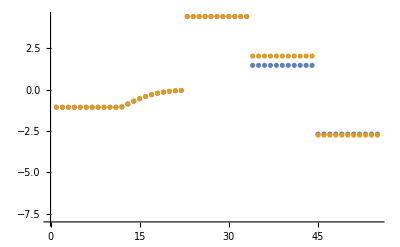

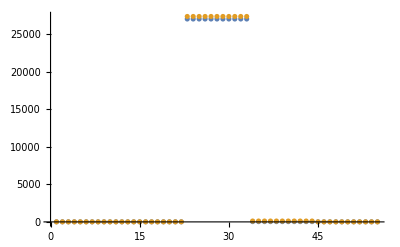

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

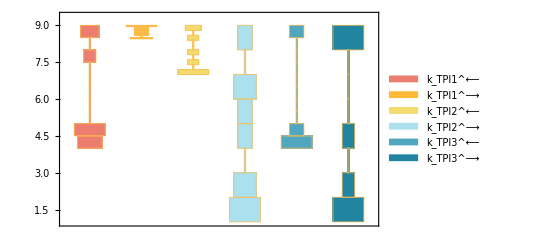

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

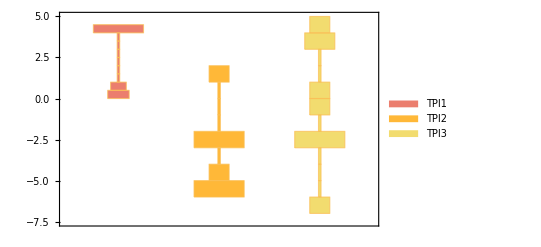

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

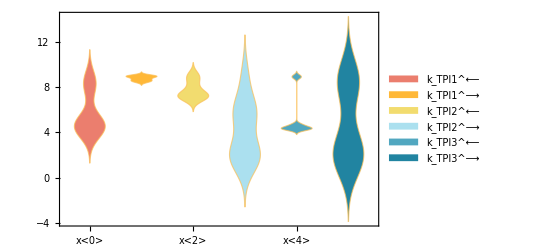

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

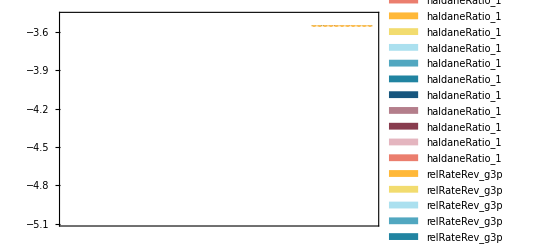

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.00103 | 0.000989425 | 3.93934

```mathematica
assumedSaturatingConc
```

1

```mathematica
PrimeQ[1]
```

False

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
27025.3 | 27403.6 | 1.39987
30.0281 | 109.395 | 264.309

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.0872761 | 0.0872999 | 0.0271693

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.0872761 | 0.0872999 | 0.0271693

```mathematica
print[inhibitionList]
```

print[inhibitionList]

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

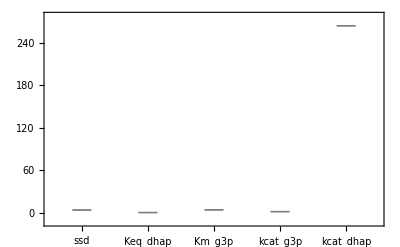

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

```mathematica
{eqnNameList,eqnValList,eqnValListPy,fileList,fileListSub}=exportRateEqs[inputPath,absoluteRateForward,absoluteRateReverse,relativeRateForward,relativeRateReverse,metsSub,metSatForSub,metSatRevSub,rateConstsSub,otherAbsoluteRatesForward,otherAbsoluteRatesReverse];
```

## Export data

```mathematica
directoryExport = "/Users/guest/Desktop/internship stuff/MASSef/examples/"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit = 4;
```

/Users/guest/Desktop/internship stuff/MASSef/examples/

CreateDirectory::filex: /Users/guest/Desktop/internship stuff/MASSef/examples/tpi already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/tpi\rateconst_labels_tpi.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/tpi\S_tpi.txt

```mathematica
"/Users/guest/Desktop/internship stuff/MASSef/examples/chors\\S_chors.txt"
```

/Users/guest/Desktop/internship stuff/MASSef/examples/chors\S_chors.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_TPI[c],E_TPI[c]&dhap,dhap[c],g3p[c],E_TPI[c]&g3p}

/Users/guest/Desktop/internship stuff/MASSef/examples/tpi\species_tpi.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{TPI1: dhap[c] + E_TPI[c] <=> E_TPI[c]&dhap,TPI2: E_TPI[c]&g3p <=> E_TPI[c] + g3p[c],TPI3: E_TPI[c]&dhap <=> E_TPI[c]&g3p}

/Users/guest/Desktop/internship stuff/MASSef/examples/tpi\reactions_tpi.txt

```mathematica
solEnz = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_TPI[c],E_TPI[c]&dhap,E_TPI[c]&g3p}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((-(k_TPI1_rev*k_TPI2_fwd*param_TPI_total) - k_TPI2_fwd*k_TPI3_fwd*param_TPI_total - k_TPI1_rev*k_TPI3_rev*param_TPI_total)/(dhap(c)*k_TPI1_fwd*k_TPI2_fwd + k_TPI1_rev*k_TPI2_fwd + g3p(c)*k_TPI1_rev*k_TPI2_rev + dhap(c)*k_TPI1_fwd*k_TPI3_fwd + k_TPI2_fwd*k_TPI3_fwd + g3p(c)*k_TPI2_rev*k_TPI3_fwd + dhap(c)*k_TPI1_fwd*k_TPI3_rev + k_TPI1_rev*k_TPI3_rev + g3p(c)*k_TPI2_rev*k_TPI3_rev))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/tpi\rateconst_clusters_tpi.txt

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["/Users/guest/Desktop/internship stuff/MASSef/examples/tpi\\rateconst_clusters_tpi.txt"]]]
```

```mathematica
solRateEq = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
```

```mathematica
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/tpi\rateLaw_tpi.txt